# Thesis Notebook

## 2D Orbit now with dissipative forces

## Setting functions up and choosing variables

## Star constants

```mathematica
(*From wikipedia paper*)
```

```mathematica
Msol = 1.989 10^30;
G = 6.6743 10^-11;
c = 3 10^8;
```

```mathematica
Mdummy = (G 1.4Msol)/c^2
```

2065.03

```mathematica
R = (16 10^3)/Mdummy
```

7.74808

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = R;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r) definitions

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2; 

rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

### Lapse and shift

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

```mathematica
rbarStar = rbarofrOutside[RStar] //  N
```

6.71082

## TOV ρ=constant Isotropic coords definitions

### Mass function

```mathematica
Mfunc[r_] = Piecewise[{{M r^3/RStar^3, r < RStar}, {M, r>=RStar}}];
```

### r(r̄), r̄(r) for the interior

```mathematica
κ = √(2 M/RStar^3);
(*Integral constant I used by hand*)
Const = rbarofrOutside[RStar] √((1+√(1-(2M)/RStar))/(1-√(1-2 M/RStar)));(*This is the constant to match up the metrics*)
```

```mathematica
rbarofrInside[r_]:=Const √((1-√(1-2 Mfunc[r]/r))/(1+√(1-2 Mfunc[r]/r)));
rofrbarInside[rbar_]:=1/κ √(1-Tanh[Log[rbar/Const]]^2);
```

### Lapse and shift functions

```mathematica
αInside[rbar_]:=(3/2 √(1-2 M/RStar)-1/2 √(1-2(M rofrbarInside[rbar]^2)/RStar^3)); (*Lapse*)
AInside[rbar_]:=rofrbarInside[rbar]/rbar;(*Shift*)
```

## Setting up everything to solve the system of ODEs in 2D with dissipative forces

### Constants used

```mathematica
m = 10^-6; (*mass of PBH*)
ρ = 3/(4Pi RStar^3);
a = 0.5; (*relativistic speed of sound*)
```

### Pressure function derived analytically

```mathematica
P[rbar_] = ρ((√(1 - 2(M r^2)/RStar^3)-√(1 - 2 M/RStar))/(3 √(1 - 2 M/RStar) - √(1 - 2(M r^2)/RStar^3))) /.r->rofrbarInside[rbar];
(*Derived from TOV as I done last year*)
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.99;
x2=1.01;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Mach_] := Piecewise[{
{1/2 Log[(1+ Mach)/(1 - Mach)] - Mach, Mach < 0.99},
{anaylticline[Mach], 0.99 < Mach  < 1.01},
{1/2 Log[1 - 1/Mach^2]  + 10, Mach > 1.01}
}];
```

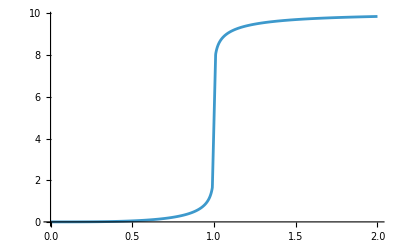

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, Exclusions->None, PlotRange->All]
```

```mathematica
DERαOutside[rbar_] := Derivative[1][α][rbar]
```

```mathematica
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERαInside[rbar_] := Derivative[1][αInside][rbar]
DERAInside[rbar_] := Derivative[1][AInside][rbar]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;
```

```mathematica
dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] := umagInside[rbar, ur, uphi]/(a αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative forces

Accretion

```mathematica
mdot[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (4Pi ρ m^2)/((a^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -4 Pi αInside[rbar](ρ + P[rbar])m^2(1/(a^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(3/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -4 Pi αInside[rbar](ρ + P[rbar])m^2(1/(a^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(3/2)uphi
```

Drag

```mathematica
dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;

dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(ρ + P[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;
```

```mathematica
dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := M r^3/RStar^3;
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
(*eccentricity = 9/11;*) (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)
semilatrecP = 7.5;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity) (*Where have you got this from Eoghan*)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[m, rbarStar,0, AngularMomentumUphi0]
duphidtInside[m, rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.000437634

-1.17526×10^-6

0.046843

```mathematica
t0=0;
tEnd=20000;
η =  2.5 10^4;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision
][[1]];
```

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

9042.7

103.385

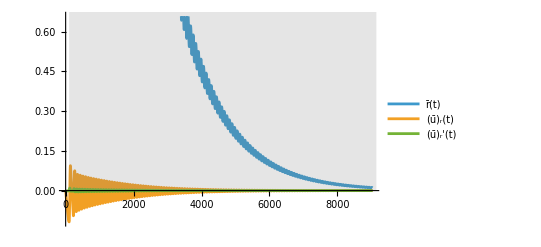

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

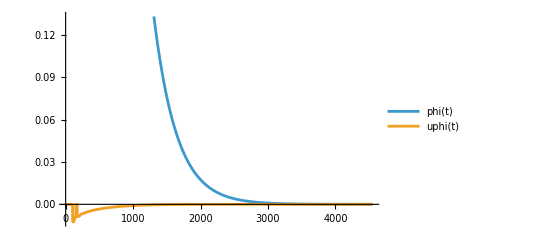

```mathematica
outFigAngular=Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

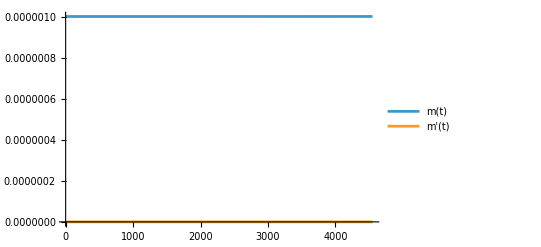

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

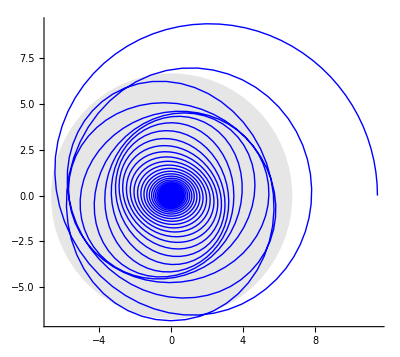

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
Show[%193,AxesStyle->Black]
```

Show::gtype: Symbol is not a type of graphics.

Show[True,AxesStyle→GrayLevel[0]]

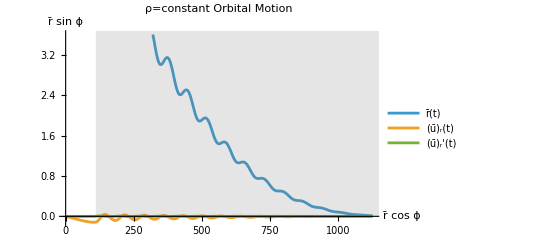

```mathematica
Show[%210,AxesLabel->{HoldForm[r̄ cos ϕ],HoldForm[r̄ sin ϕ]},PlotLabel->HoldForm[ρ=constant Orbital Motion],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/em/Documents/thesis/constant_density/eta=3OrbMotion.jpg",%211,"JPEG"]
```

/home/em/Documents/thesis/constant_density/eta=3OrbMotion.jpg

```mathematica
FRRrFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRr[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRrIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

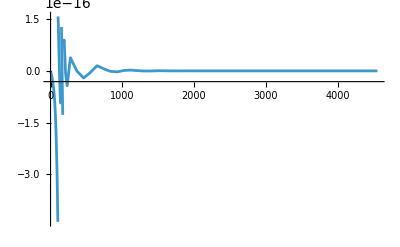

```mathematica
Plot[FRRrFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

```mathematica
FRRphiFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{FRRphi[m, rbar, ur, uphi], rbar >= rbarStar},
{FRRphiIns[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

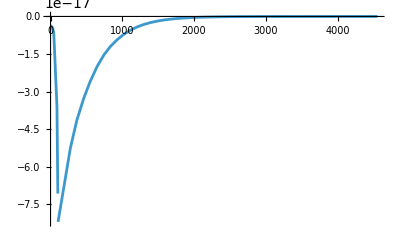

```mathematica
Plot[FRRphiFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

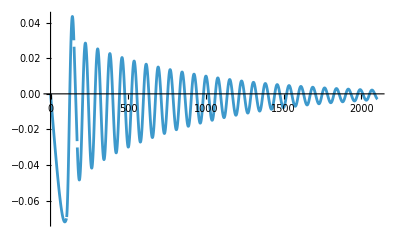

```mathematica
Plot[
{
Piecewise[
{
{drBardt[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{drBardtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

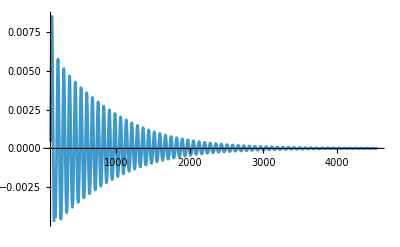

```mathematica
Plot[
{
Piecewise[
{
{durdt2DOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{durdt2DInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tFinish}, PlotRange->All
]
```

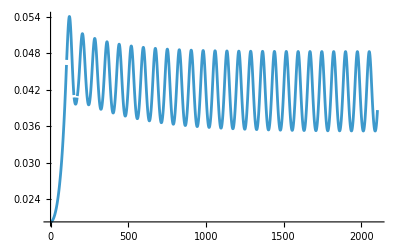

```mathematica
Plot[
{
Piecewise[
{
{dphidtOutside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]>=rbarStar},
{dphidtInside[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

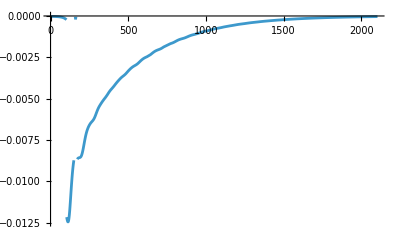

```mathematica
Plot[
{
Piecewise[
{
{duphidtOutside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]], rbarNumIn[t]>=rbarStar},
{duphidtInside[massNumIn[t], rbarNumIn[t],urNumIn[t],uphiNumIn[t]],rbarNumIn[t]<rbarStar}
}
]
},
{t,0,tSurface+2000}, PlotRange->All
]
```

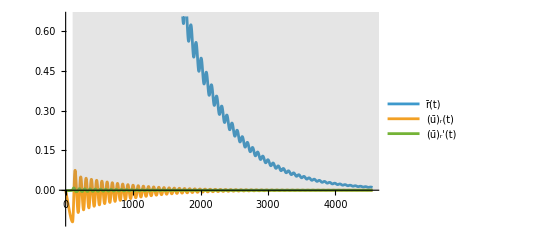

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

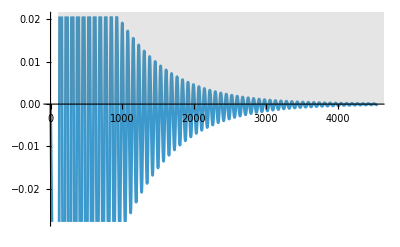

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

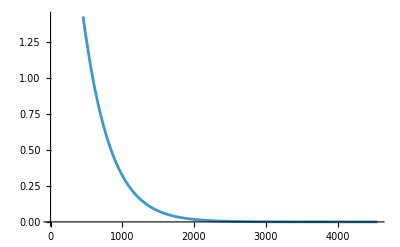

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

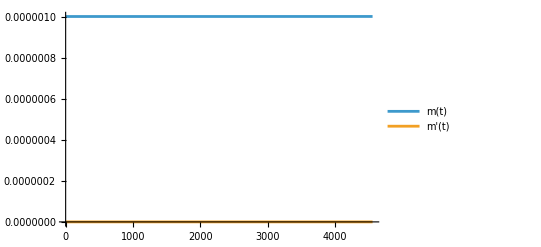

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

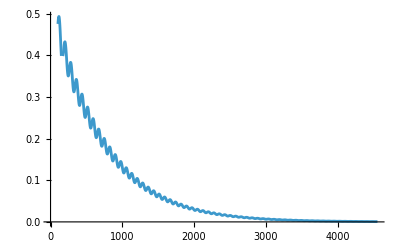

```mathematica
Plot[umag[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, Exclusions->None]
```

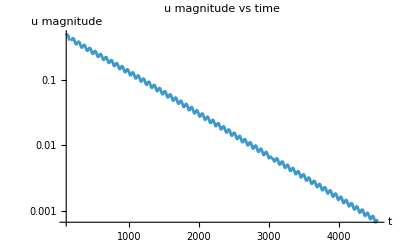

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
(*Show me the value of u at tfinish*)
umag[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn
```

0.000732419

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((Mfunc[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

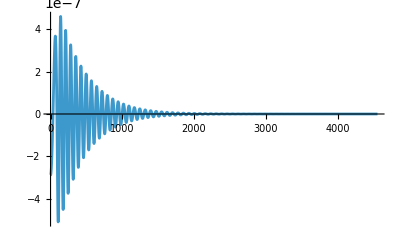

```mathematica
Plot[hplusFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

```mathematica
Show[%277,AxesLabel->{HoldForm[time],HoldForm[SubPlus[h]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,AxesLabel→{time,h_+},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((Mfunc[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

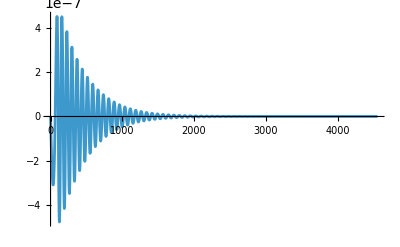

```mathematica
Plot[hxFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None]
```

```mathematica
Show[%284,AxesLabel->{HoldForm[time],HoldForm[Subscript[h, x]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,AxesLabel→{time,h_x},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

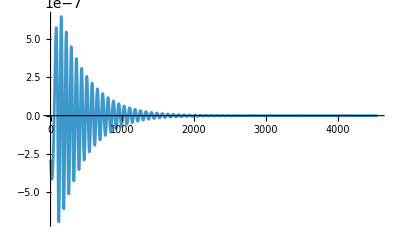

```mathematica
Plot[hplusFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]]+hxFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

## Energy loss during orbits CHECK angles and other assumptions made by authors for these formulae especially the angular momentum stuff.

### Instantaneous energy loss (coordinate system dependent)

```mathematica
dEdtInside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarInside[rbar],rd,phid},rd=drBardtInside[rbar,ur,uphi];
phid=dphidtInside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(MassFunction[r]^2*(8 rd^2+6 (r phid)^2)+r MassFunction[r]*(6 rd^4-6 (3(r phid)^4+(r phid)^2 Mp[r])+rd^2 (63 (r phid)^2+Mp[r]-3 r Mpp[r]))+r^2*(6 (r phid)^4 Mp[r]-rd^2 ((Mp[r])^2+3 (r phid)^2 (13 Mp[r]-3 r Mpp[r]))-rd^4 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))]
```

```mathematica
dEdtOutside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarOutside[rbar],rd,phid},rd=drBardt[rbar,ur,uphi];
phid=dphidtOutside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(M^2*(8 rd^2+6 (r phid)^2)+r M*(6 rd^4-6 (3(r phid)^4)+rd^2 (63 (r phid)^2)))]
```

```mathematica
dEdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dEdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dEdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

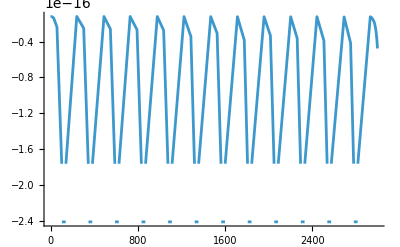

```mathematica
Plot[dEdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

### Average, physical energy loss per orbit

```mathematica
dEdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^3)/(5 a^5 (1-e^2)^(7/2))*(1+(73/24) e^2+(37/96) e^4)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t)

## Angular momentum loss during orbits

### Instantaneous angular momentum loss (coordinate system dependent)

```mathematica
dLdt[m_,M_,a_,e_, phi_]:= -(4(m^2 M^(5/2)))/(5(a^(7/2)(1-e^2)^(7/2)))(1 + e Cos[phi])^3 (8 - 3 e^2 + 20e Cos[phi] + 15 e^2 Cos[2phi])
```

```mathematica
Plot[dLdt[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

-Graphics-

### Average, physical angular momentum loss per orbit

```mathematica
(*Formula might need to be adjusted for me as they use the angle phi = 0 for when it crosses the star surface which is not true for me*)
```

```mathematica
dLdtAvg[m_,M_,a_,e_]:=-(32 m^2 M^(5/2))/(5 a^(7/2) (1-e^2)^(2))*(1+(7/8) e^2)
```

Need formulae for M[t]? Although accretion is very small. a(t) and e(t).

Use E and L to find a(t) and e(t)??

## Converting back to the areal radius to see the 2D graph and if it is different

```mathematica
(*Areal radius as a function of isotropic radius*)rFromRbar[rbar_]:=Piecewise[{{A[rbar]*rbar,rbar>=rbarStar},(*exterior*){AInside[rbar]*rbar,rbar<rbarStar}    (*interior*)}];

(*Areal radius along the orbit*)
arealr[t_]:=rFromRbar[rbarNumIn[t]];
```

```mathematica
x[t_]:=arealr[t] Cos[phiNumIn[t]];
y[t_]:=arealr[t] Sin[phiNumIn[t]];
```

```mathematica
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->1,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
```

```mathematica
(*Areal radius of the stellar surface*)
rstarAreal=A[rbarStar] rbarStar;

centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rstarAreal]}];
```

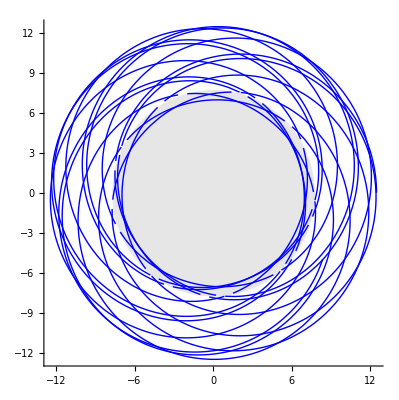

```mathematica
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

discontinuity here at the edge, not sure why?